{{ψ→InterpolatingFunction[{{0., 15.}, {…, -60., 60., …}}, <>]}}

-Graphics-

-Graphics-

-Graphics-

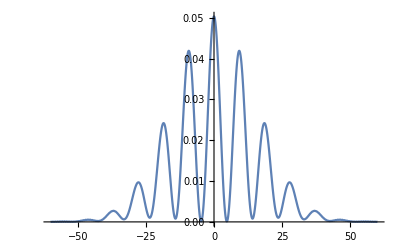

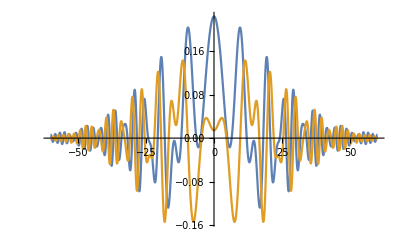

```mathematica
ћ=1;
m=1;
z=5;
ψ0=(ⅇ^(z^2) (ⅇ^(-(-z+x)^2)+ⅇ^(-(z+x)^2)))/(√(1+ⅇ^(2 z^2)) (2 π)^(1/4));
s=NDSolve[{I*ћ*D[ψ[t,x],t]==-((ћ^2)/(2*m))*D[ψ[t,x],x,x],ψ[t,-60]==ψ[t,60],ψ[0,x]==ψ0},ψ,{t,0,15},{x,-60,60},AccuracyGoal->10]

DensityPlot[Abs[ψ[t,x]]^2/.s,{t,0,15},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Re[ψ[t,x]]]/.s,{t,0,15},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Im[ψ[t,x]]]/.s,{t,0,15},{x,-60,60},PlotPoints->250]
Plot[Abs[ψ[15,x]]^2/.s,{x,-60,60},PlotPoints->250,PlotRange->Full]
Plot[{Re[ψ[15,x]]/.s,Im[ψ[15,x]]/.s},{x,-60,60},PlotPoints->250,PlotRange->Full]
```